```mathematica
Clear["Global`*"]
```

1 - 10 Data representations
Represent the data by a stem-and-leaf plot, a histogram, and a boxplot:

1.  Length of nails [mm] 19, 21, 19, 20, 19, 20, 21, 20

```mathematica
ln={19,21,19,20,19,20,21,20}
```

{19,21,19,20,19,20,21,20}

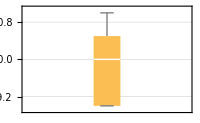

```mathematica
bwc=BoxWhiskerChart[{ln},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

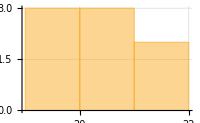

```mathematica
his=Histogram[{ln},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
StemLeafPlot[ln]
```

Stem | Leaves
1 | 999
2 | 00011
Stem units: 10

3.  Systolic blood pressure of 15 female patients of ages 20-22
156, 158, 154, 133, 141, 130, 144, 137, 151, 146, 156, 138, 138, 149, 139

```mathematica
sbp={156,158,154,133,141,130,144,137,151,146,156,138,138,149,139}
```

{156,158,154,133,141,130,144,137,151,146,156,138,138,149,139}

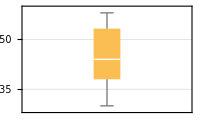

```mathematica
bwc=BoxWhiskerChart[{sbp},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

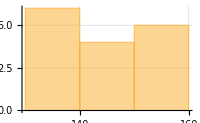

```mathematica
his=Histogram[{sbp},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

```mathematica
StemLeafPlot[sbp]
```

Stem | Leaves
1 | 334444445555666
Stem units: 100

5.  Weight of filled bags [g] in an automatic filling
203, 199, 198, 201, 200, 201, 201

```mathematica
wb={203,199,198,201,200,201,201}
```

{203,199,198,201,200,201,201}

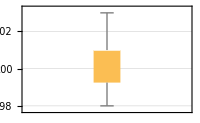

```mathematica
bwc=BoxWhiskerChart[{wb},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

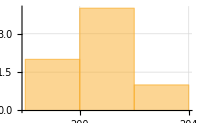

```mathematica
his=Histogram[{wb},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

```mathematica
StemLeafPlot[wb]
```

Stem | Leaves
2 | 0000000
Stem units: 100

7.  Release time [sec] of a relay
1.3, 1.2, 1.4, 1.5, 1.3, 1.3, 1.4, 1.1, 1.5, 1.4, 1.6, 1.3, 1.5, 1.1, 1.4, 1.2, 1.3, 1.5, 1.4, 1.4

```mathematica
rt={1.3,1.2,1.4,1.5,1.3,1.3,1.4,1.1,1.5,1.4,1.6,1.3,1.5,1.1,1.4,1.2,1.3,1.5,1.4,1.4}
```

{1.3,1.2,1.4,1.5,1.3,1.3,1.4,1.1,1.5,1.4,1.6,1.3,1.5,1.1,1.4,1.2,1.3,1.5,1.4,1.4}

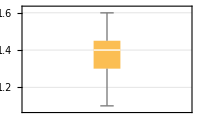

```mathematica
bwc=BoxWhiskerChart[{rt},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

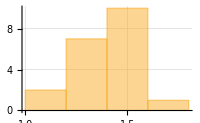

```mathematica
his=Histogram[{rt},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

```mathematica
StemLeafPlot[rt]
```

Stem | Leaves
1 | 11223333344444455556
Stem units: 1

9.  Efficiency [%] of seven Voith Francis turbines of runner diameter 2.3 m under a head range of 185 m
91.8, 89.1, 89.9, 92.5, 90.7, 91.2, 91.0

```mathematica
eff={91.8,89.1,89.9,92.5,90.7,91.2,91.0}
```

{91.8,89.1,89.9,92.5,90.7,91.2,91.}

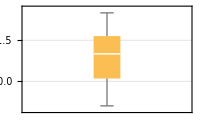

```mathematica
bwc=BoxWhiskerChart[{eff},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

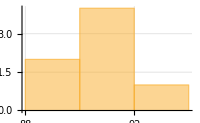

```mathematica
his=Histogram[{eff},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

```mathematica
StemLeafPlot[eff]
```

Stem | Leaves
8 | 9
9 | 011122
Stem units: 10

10.  -0.51, 0.12, -0.47, 0.95, 0.25, -0.18, -0.54

```mathematica
nn={-0.51,0.12,-0.47,0.95,0.25,-0.18,-0.54}
```

{-0.51,0.12,-0.47,0.95,0.25,-0.18,-0.54}

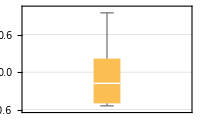

```mathematica
bwc=BoxWhiskerChart[{nn},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

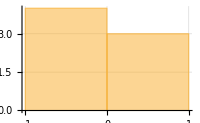

```mathematica
his=Histogram[{nn},FrameLabel->Automatic,GridLines->Automatic,ImageSize->200]
```

```mathematica
StemLeafPlot[nn]
```

Stem | Leaves
-5 | 41
-4 | 7
-1 | 8
1 | 2
2 | 5
9 | 5
Stem units: 1/10

11 - 16 Average and spread
Find the mean and compare it with the median. Find the standard deviation and compare it with the interquartile range.

11.  For the data in problem 1.

```mathematica
Grid[N[{{"Mean","Median","Standard Deviation","Interquartile Range"},{Mean[ln],Median[ln],StandardDeviation[ln],InterquartileRange[ln]}}],Frame->All]
```

Mean | Median | Standard Deviation | Interquartile Range
19.875 | 20. | 0.834523 | 1.5

13.  For the medical data in problem 3.

```mathematica
Grid[N[{{"Mean","Median","Standard Deviation","Interquartile Range"},{Mean[sbp],Median[sbp],StandardDeviation[sbp],InterquartileRange[sbp]}}],Frame->All]
```

Mean | Median | Standard Deviation | Interquartile Range
144.667 | 144. | 8.97351 | 15.25

15.  For the release times in problem 7.

```mathematica
Grid[N[{{"Mean","Median","Standard Deviation","Interquartile Range"},{Mean[rt],Median[rt],StandardDeviation[rt],InterquartileRange[rt]}}],Frame->All]
```

Mean | Median | Standard Deviation | Interquartile Range
1.355 | 1.4 | 0.135627 | 0.15

17.  Outlier, reduced data. Calculate s for the data 4, 1, 3, 10, 2. Then reduce the data by deleting the outlier and calculate s. Comment.

```mathematica
Grid[N[{{"Standard Deviation","Stand Dev w/o Outlier"},{StandardDeviation[{4,1,3,10,2}],StandardDeviation[{4,1,3,2}]}}],Frame->All]
```

Standard Deviation | Stand Dev w/o Outlier
3.53553 | 1.29099